-Graphics-

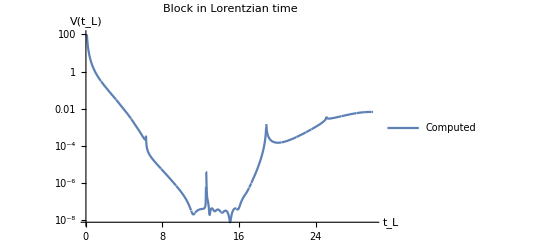

-Graphics-

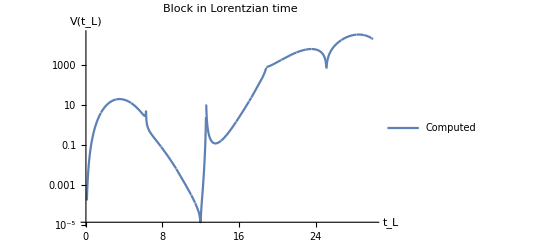

-Graphics-

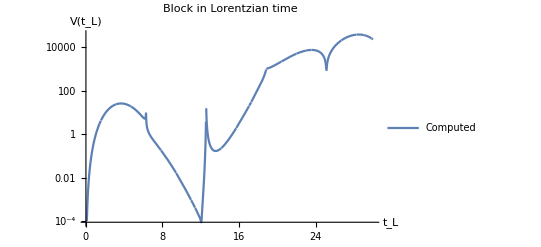

-Graphics-

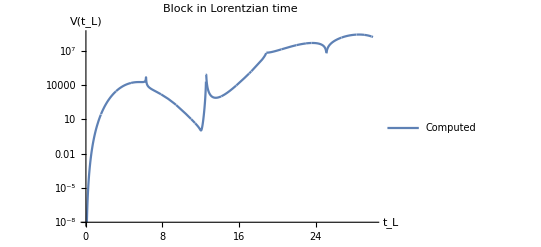

-Graphics-

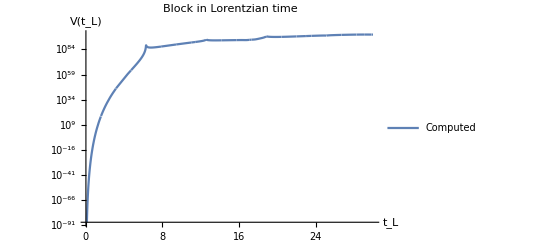

-Graphics-

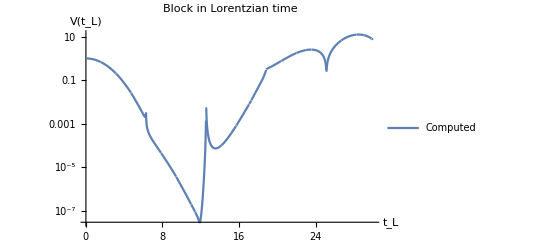

-Graphics-

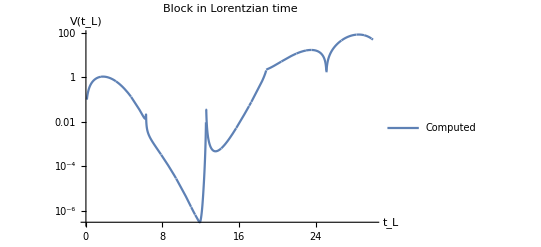

-Graphics-

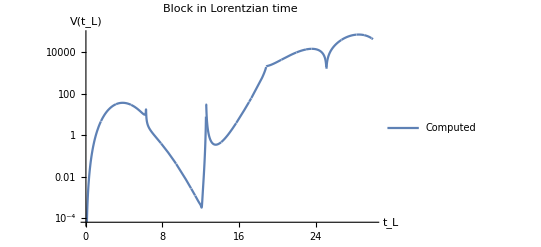

-Graphics-

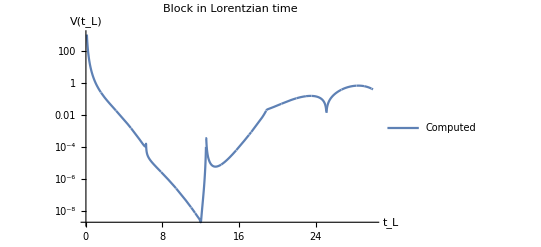

-Graphics-

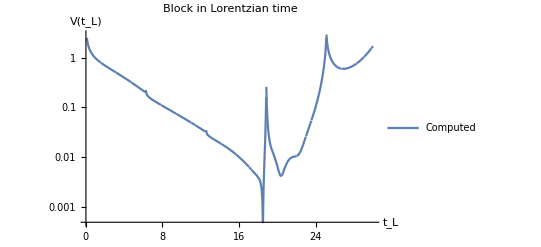

-Graphics-

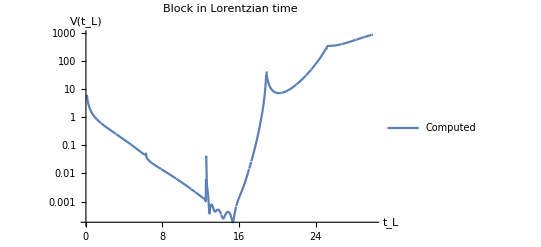

-Graphics-

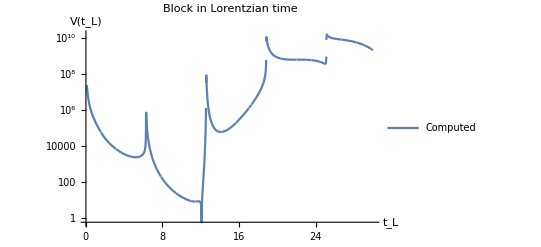

```mathematica
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"Virasoro.m"];

results1=VRun[30,1,3,0,200];
results2=VRun["testruns.txt"];
VWrite[results2,"testruns_results.txt"];
r=0.99; (*r used in map from q to Subscript[t, L]*)
VPlot[results1,1,1,r];
VPlot[results2,1,1,r];
```